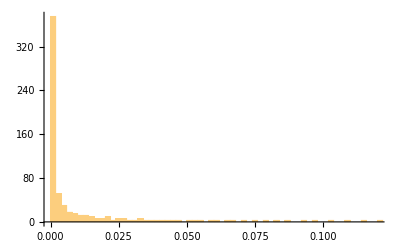

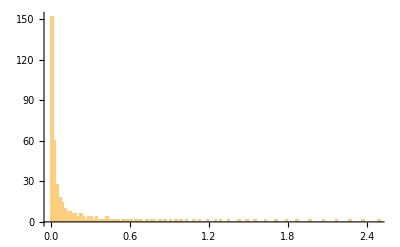

```mathematica
relwHe=Import["/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v4/basis_struct/relw3heLIT_J0.5_npp0.5^+.dat","Table"];
relwEnd=Import["/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v4/basis_struct/relw3heLIT_J0.5_0.5^-.dat","Table"];
Histogram[Flatten[relwEnd],200]
Histogram[Flatten[relwHe],200]
```

```mathematica
wd[x_,α_,β_,γ_,n_]:=-(γ x+α)^n+β;
```

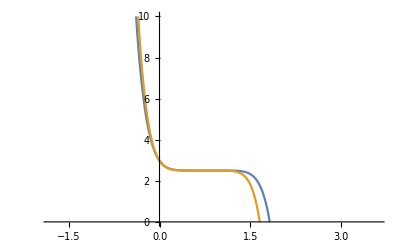

```mathematica
ng=7;
al=-0.9;
be=2.5;
ga=1.12;
Plot[{wd[x,al,be,ga,ng],wd[x,al,be,1.1 ga,ng]},{x,-2 Abs[al],4 Abs[al]},PlotRange->{Automatic,{0,10}}]
```

```mathematica
width={Subscript[σ, 1],Subscript[σ, 2]};
cntr={Subscript[α, 1],Subscript[α, 2]};
Total[Table[Exp[-width[[mm]] (x-cntr[[mm]])^2],{mm,1,Length[width]}]]/Total[Sqrt[Pi/width]]
```

(ⅇ^(-(x-α_1)^2 σ_1)+ⅇ^(-(x-α_2)^2 σ_2))/(√π √(1/σ_1)+√π √(1/σ_2))

```mathematica
Integrate[Exp[-a (x-centr)^2]+Exp[-b (x-2 centr)^2],{x,-Infinity,Infinity},Assumptions->{centr∈Reals,n>0,n∈Integers,a∈Reals,b∈Reals,a>0,b>0}]
```

(1/(√a)+1/(√b)) √π

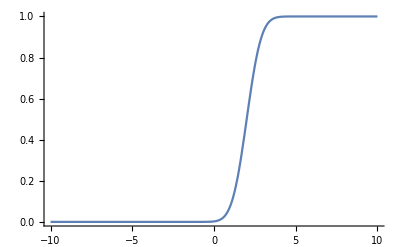

```mathematica
gcenters={2};
gwidths={1};
Cum[xm_?NumericQ,cntr_?ArrayQ,width_?ArrayQ]:=NIntegrate[Total[Table[Exp[-width[[mm]] (x-cntr[[mm]])^2],{mm,1,Length[width]}]]/Total[Sqrt[Pi/width]],{x,-Infinity,xm}];
Plot[Cum[xx,gcenters,gwidths],{xx,-10,10},PlotRange->All]
```

{0.0906988,0.482642,0.812474,1.09367,1.33882,1.56004,1.76793,1.97206,2.18259,2.41345,2.69031,3.07947,3.75284,4.37832,4.78977,5.15368,5.57625,10.6181}

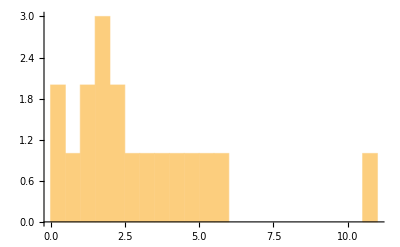

```mathematica
anz=20;
gcenters={1,2,5};
gwidths={0.2,1,1};
basisW=Select[Table[c/.FindRoot[Cum[c,gcenters,gwidths]==dy,{c,0.1}],{dy,Subdivide[0,1.,anz]}],#>0&]
Histogram[basisW,20]
```

```mathematica
ss={Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]};
bb={Subscript[α, 1],Subscript[α, 2],Subscript[α, 3]};
Total[Table[Sqrt[ss[[n]]/Pi] Exp[-ss[[n]] (x-bb[[n]])^2],{n,Length[ss]}]]
Integrate[Total[Table[Sqrt[ss[[n]]/Pi] Exp[-ss[[n]] (x-bb[[n]])^2],{n,Length[ss]}]]/Length[ss],{x,-Infinity,Infinity},Assumptions->{Subscript[σ, 1]∈Reals,Subscript[σ, 1]>0,Subscript[α, 1]∈Reals,Subscript[σ, 2]∈Reals,Subscript[σ, 2]>0,Subscript[α, 2]∈Reals,Subscript[σ, 3]∈Reals,Subscript[σ, 3]>0,Subscript[α, 3]∈Reals}]
```

(ⅇ^(-(x-α_1)^2 σ_1) √σ_1)/(√π)+(ⅇ^(-(x-α_2)^2 σ_2) √σ_2)/(√π)+(ⅇ^(-(x-α_3)^2 σ_3) √σ_3)/(√π)

1

```mathematica
Cum[xm_?NumericQ,cntr_?ArrayQ,width_?ArrayQ]:=NIntegrate[Total[Table[Sqrt[width[[mm]]/Pi] Exp[-width[[mm]] (x-cntr[[mm]])^2],{mm,1,Length[width]}]]/Length[width],{x,-100,xm}];
```

```mathematica
gcenters
gwidths
```

{2}

{1}

```mathematica
widthEq[vv_?NumericQ,cntr_?ArrayQ,width_?ArrayQ,cc_?NumericQ]:=
Total[Table[Erf[Sqrt[width[[mm]]] (vv-cntr[[mm]])],{mm,1,Length[width]}]]-(2 cc-1) Length[width]
```

```mathematica
anz=10;
Select[Table[vv/.FindRoot[widthEq[vv,gcenters,gwidths,cc],{vv,8.51}],{cc,Subdivide[0.,1.,anz]}],#≥0&]
```

{8.51,8.51,8.51,8.51,8.51,8.51,8.51,8.51,8.51,8.51,8.51}

```mathematica
Subdivide[0.,1.,anz]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Integrate[Sqrt[α/Pi] Exp[-α (x-β)^2],{x,-Infinity,Infinity},Assumptions->{α∈Reals,α>0,β∈Reals}]
```

1

```mathematica
Integrate[Sqrt[α/Pi] Exp[-α (x-β)^2],{x,-Infinity,y},Assumptions->{α∈Reals,α>0,β∈Reals}]
```

1/2 (1+Erf[√α (y-β)])

```mathematica
FindRoot[Cum[c,{2},{1}]==0.25,{c,0.1}]
```

{c→1.52306}